```mathematica
ClearAll["Global`*"];
```

```mathematica
(*5Dz1*)
d=5;
bargtt=(l^2)/(r^2-M l^2); (*gtt barra é o negativo de gtt metrica up*)
grr=(r^2-M l^2)/(l^2);
gxx=l^2/r^2;
Gtt=(3M l^2-6r^2)/(r^4-M l^2r^2); (*tensor de einstein*)
Grr=-9M/l^2 +3M^2/r^2 +6r^2/l^4;
Gxx=(6r^2-M l^2)/r^4;
alfa=η(3M l^2-6r^2)/(r^2l^2)//FullSimplify;
beta=(η l^2)/(r^2-M l^2)(3M^2/r^2+6r^2/l^4-9M/l^2)//FullSimplify;
b=r^((2-d)/2)((1-alfa)(1+beta))^(-1/4)//FullSimplify;
FullSimplify[db=D[b,r]];
ddb=D[db,r]//FullSimplify;
R=-20/l^2+6M/r^2; (*escalar de ricci*)
barhtt=bargtt-η Gtt; (*htt barra é o negativo de htt metrica efetica up*) (*η = constante de acoplamento*)
hrr=grr+η Grr;
hxx=gxx+η Gxx;
dhrr=D[hrr,r]//FullSimplify;
H=hrr/barhtt//FullSimplify;
C5=(H/b)(ddb+db((dhrr/hrr)+((d-2)/r) ))//FullSimplify; (*termo aditivo ao potencial*)
η=0;
ξ=0;
κ=0;
l=1;
m=0;
Collect[V=(hxx κ^2+m^2+ξ R)/(barhtt)-C5//FullSimplify,{r}]
VBTZ=(r^2-M l^2)/(l^2+η)(m^2-(6 ξ)/l^2+κ^2/r^2+κ^2/(r^2 l^2))+(3 r^2)/(4 l^2)-M/(2 l^2)-M^2/(4 r^2)
FullSimplify[V-VBTZ]
```

-(9 M)/2+(3 M^2)/(4 r^2)+(15 r^2)/4

-M/2-M^2/(4 r^2)+(3 r^2)/4

-4 M+M^2/r^2+3 r^2

```mathematica
Collect[Vnumerador=-(l^2 M-r^2) (540 r^6 η^2+4 l^8 (r^2-3 M η) (r^2-M η) κ^2+l^6 (4 m^2 r^6+9 M^3 η^2+48 r^4 η κ^2-3 M (32 r^2 η^2 κ^2+r^4 (1+4 m^2 η-8 ξ))+18 M^2 r^2 η (1-4 ξ))-12 l^2 r^4 η (42 M η+5 r^2 (-3+8 ξ))+l^4 (135 M^2 r^2 η^2+r^6 (15+24 m^2 η-80 ξ)+6 r^4 η (-17 M+24 η κ^2+64 M ξ))),{r}];
Collect[Vdenominador=4 l^4 (6 r^3 η+l^2 (r^3-3 M r η))^2//Simplify,{r}];
(*Collect[V=(hxx κ^2+m^2+ξ R)/(barhtt)-C5//Simplify,{ξ,m,κ}]  *)
Vzerozerozero=Collect[-((l^2 M-r^2) (-3 l^6 M r^4+15 l^4 r^6+18 l^6 M^2 r^2 η-102 l^4 M r^4 η+180 l^2 r^6 η+9 l^6 M^3 η^2+135 l^4 M^2 r^2 η^2-504 l^2 M r^4 η^2+540 r^6 η^2))/(4 l^4 (6 r^3 η+l^2 (r^3-3 M r η))^2)//Expand,{η}];
```

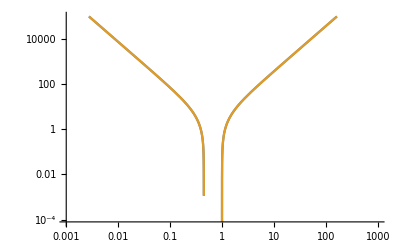

```mathematica
LogLogPlot[{-((l^2 M-r^2) (-3 l^6 M r^4+15 l^4 r^6+18 l^6 M^2 r^2 η-102 l^4 M r^4 η+180 l^2 r^6 η+9 l^6 M^3 η^2+135 l^4 M^2 r^2 η^2-504 l^2 M r^4 η^2+540 r^6 η^2))/(4 l^4 (6 r^3 η+l^2 (r^3-3 M r η))^2)/.{M-> 1,l-> 0.1,η-> 0},-((l^2 M-r^2) (-3 l^6 M r^4+15 l^4 r^6+18 l^6 M^2 r^2 η-102 l^4 M r^4 η+180 l^2 r^6 η+9 l^6 M^3 η^2+135 l^4 M^2 r^2 η^2-504 l^2 M r^4 η^2+540 r^6 η^2))/(4 l^4 (6 r^3 η+l^2 (r^3-3 M r η))^2)/.{M-> 1,l-> 0.1,η-> 0.0001}},{r,0.001,1000},PlotRange-> {-100000,100000}]
```

```mathematica
V1=-((l^2 M-r^2) (-3 l^6 M r^4+15 l^4 r^6+18 l^6 M^2 r^2 η-102 l^4 M r^4 η+180 l^2 r^6 η+9 l^6 M^3 η^2+135 l^4 M^2 r^2 η^2-504 l^2 M r^4 η^2+540 r^6 η^2))/(4 l^4 (6 r^3 η+l^2 (r^3-3 M r η))^2)/.{M-> 1,l-> 0.0001,η-> 0}
V2=-((l^2 M-r^2) (-3 l^6 M r^4+15 l^4 r^6+18 l^6 M^2 r^2 η-102 l^4 M r^4 η+180 l^2 r^6 η+9 l^6 M^3 η^2+135 l^4 M^2 r^2 η^2-504 l^2 M r^4 η^2+540 r^6 η^2))/(4 l^4 (6 r^3 η+l^2 (r^3-3 M r η))^2)/.{M-> 1,l-> 0.0001,η-> 1000000000}
```

-((1-r^2) (-3 r^4+15 r^6))/(4 r^6)

-((1-r^2) (-3 r^4+15 r^6))/(4 r^6)

```mathematica
diff=-(V1-V2)
```

0

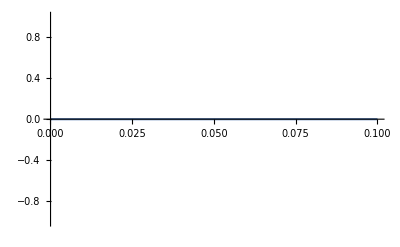

```mathematica
Plot[diff,{r,0.0001,0.1}]
```